```mathematica
(*vorts="vorts"<>ToString[#]&/@Range[99];*)
(*vorts="vorts"<>ToString[#]<>"_static"&/@Range[99];*)
(*vorts=("vorts"<>ToString[#]<>"_optimized_parallelsearch"&)/@Range[99];*)
dname="vorts";
dindex=1;
postfixes={"","_static","_optimized_parallelsearch"};
labels={": naive TF",": TF optimized for first frame",": TF optimized for each frame"};
```

```mathematica
ComputeCharts[dname_,dindex_,postfixes_,labels_]:=Module[{postfix,label,vorts,path,datanames,xml,tfifile,volumefile,legends,face,imagefilenames,txtfilenames,featurefilename,visibilityfilename,resultxml,imagefile,rawfile,dataname,plotpath,imagepath,tf,bincount,intensity,r,g,b,a,rgbcolors,rgbfunction,rgba,rgbafunction,alpha,pos,index,chartcolors,intensity0,alpha0,rangeOfAlpha,index0,scoremap,plot1,plot2,plot3,plot4,saliencemap,saliencemapxml},
postfix=postfixes[[dindex]];
label=labels[[dindex]];
vorts=(dname<>ToString[#]<>postfix&)/@Range[99];
path=NotebookDirectory[]<>"~images\\";
datanames=(dname<>ToString[#]<>postfix&)/@Join[Range[1,23],Range[25,99]];
xml=Import[path<>First@datanames<>".xml"];
{tfifile,volumefile,legends,face,imagefilenames,txtfilenames,{featurefilename,visibilityfilename},resultxml,imagefile,rawfile,dataname,plotpath,imagepath}=xml;
tf=Import[tfifile,"XML"];
bincount=256;
intensity=ToExpression@Cases[tf,XMLElement["intensity",{"value"->atrib_,___},___]:>atrib,∞];
r=ToExpression@Cases[tf,XMLElement["colorL",{"r"->atrib_,___},___]:>atrib,∞];
g=ToExpression@Cases[tf,XMLElement["colorL",{___,"g"->atrib_,___},___]:>atrib,∞];
b=ToExpression@Cases[tf,XMLElement["colorL",{___,"b"->atrib_,___},___]:>atrib,∞];
a=ToExpression@Cases[tf,XMLElement["colorL",{___,"a"->atrib_},___]:>atrib,∞];
rgbcolors=(#/255.&)/@Transpose[{r,g,b}]//(RGBColor/@#&);
rgbfunction=(Blend[Transpose[{intensity,rgbcolors}], #1] & );
rgba=(#/255.&)/@Transpose[{r,g,b,a}]//(RGBColor/@#&);
rgbafunction=(Blend[Transpose[{intensity,rgba}], #1] & );
alpha=(#/255.&)/@a;

pos=intensity[[#]]&/@Flatten@Position[alpha,_?(#==0&)];
index=Flatten@Position[alpha,_?(#>0&)];
chartcolors=rgbcolors[[#]]&/@index;
intensity0=intensity;
alpha0=alpha;
rangeOfAlpha=Range[Length[alpha]];
If[First[intensity0]>0,intensity0=Join[{0},intensity0];alpha0=Join[{0},alpha0];rangeOfAlpha+=1];
If[Last[intensity0]<1,intensity0=Join[intensity0,{1}];alpha0=Join[alpha0,{0}]];
index0=Flatten@Position[alpha0,_?(#>0&)];

resultxml="D:\\document\\work\\time-varying-visualization\\~images\\saliency.xml";
scoremap=If[FileExistsQ[resultxml],Association@Import[resultxml],<||>];
plot1=ListLinePlot[Table[scoremap[#][[1]][[i]]&/@datanames,{i,Range[3]}],PlotLegends->{"Feature 1","Feature 2","Feature 3"},PlotLabel->"Feature saliency"<>label,AxesLabel->{"Time step","Saliency"},PlotRange->{Automatic,{0,1}},PlotStyle->chartcolors];
plot2=ListLinePlot[Table[scoremap[#][[2]][[i]]&/@datanames,{i,Range[3]}],PlotLegends->{"Feature 1","Feature 2","Feature 3"},PlotLabel->"Feature visibility"<>label,AxesLabel->{"Time step","FV"},PlotRange->{Automatic,{0,1}},PlotStyle->chartcolors];
plot3=ListLinePlot[Table[scoremap[#][[5]][[i]]&/@datanames,{i,Range[3]}],PlotLegends->{"Feature 1","Feature 2","Feature 3"},PlotLabel->"Visibility-weighted saliency (VWS)"<>label,AxesLabel->{"Time step","VWS"},PlotRange->{Automatic,{0,1}},PlotStyle->chartcolors];
(*Export[plotpath<>dname<>postfix<>".png",plot3];*)
saliencemapxml="D:\\document\\work\\time-varying-visualization\\~saliencemap\\saliencemap.xml";
saliencemap=If[FileExistsQ[saliencemapxml],Association@Import[saliencemapxml],<||>];
plot4=ListLinePlot[Table[saliencemap[#][[i]]&/@datanames,{i,Range[3]}],PlotLegends->{"Feature 1","Feature 2","Feature 3"},PlotLabel->"2D feature saliency"<>label,AxesLabel->{"Time step","2DFS"},PlotRange->{Automatic,{0,1}},PlotStyle->chartcolors];
{plot1,plot2,plot3,plot4}
]
```

```mathematica
{plots1,plots2,plots3}=Table[ComputeCharts[dname,i,postfixes,labels],{i,Range[Length[postfixes]]}];
```

## Curves of the 3 saliency metrics for the visualization of the vortex data set

### Using a naive transfer function

The first one is the 3D feature saliency field (Kim & Varshney 2006)

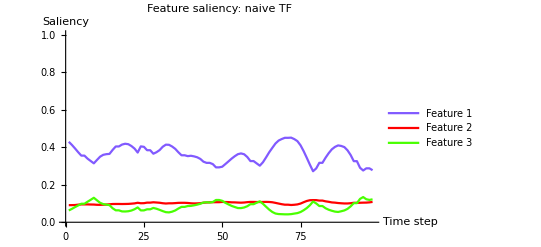

```mathematica
plots1[[1]]
```

The second one is the feature visibility (Wang et al. 2011)

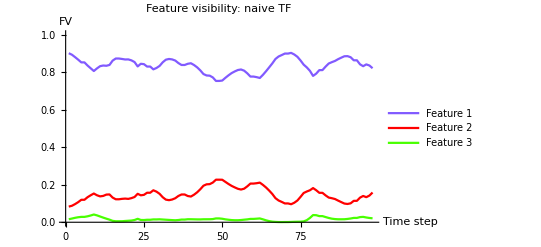

```mathematica
plots1[[2]]
```

The third one is our visibility-weighted saliency

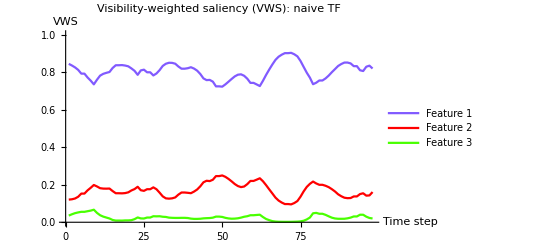

```mathematica
plots1[[3]]
```

The fourth one is the 2D feature saliency - saliency maps (Itti et al. 1998) with inverse distance weighting

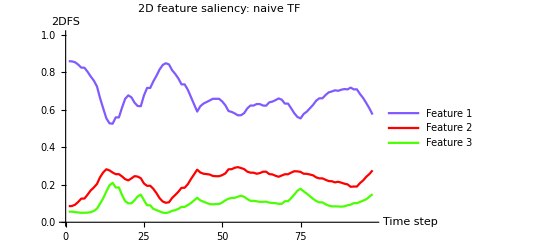

```mathematica
plots1[[4]]
```

### Using a static transfer function optimized for the first frame

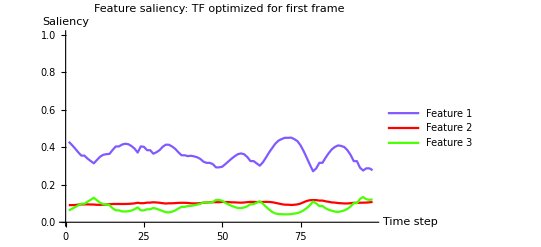

```mathematica
plots2[[1]]
```

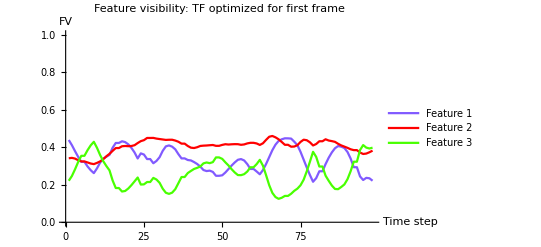

```mathematica
plots2[[2]]
```

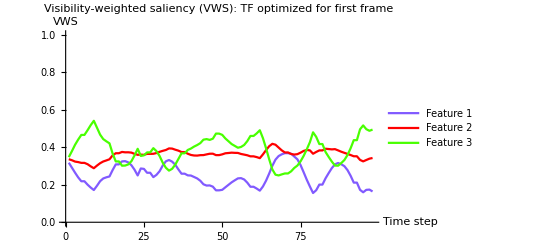

```mathematica
plots2[[3]]
```

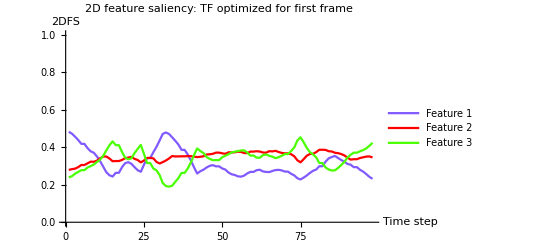

```mathematica
plots2[[4]]
```

### Using a dynamic transfer function optimized for each frame

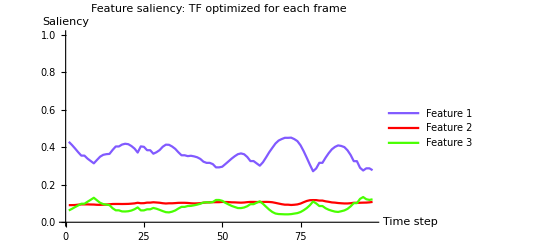

```mathematica
plots3[[1]]
```

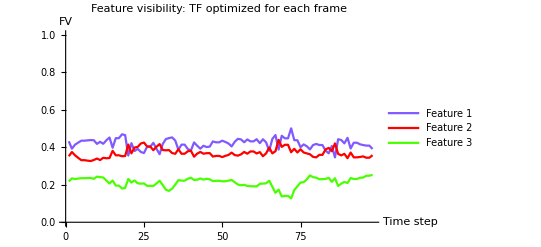

```mathematica
plots3[[2]]
```

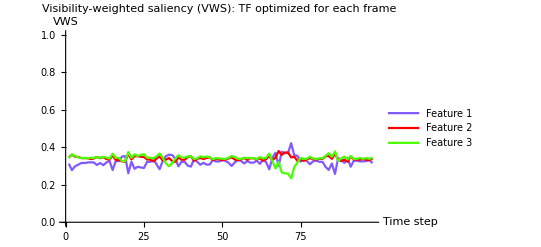

```mathematica
plots3[[3]]
```

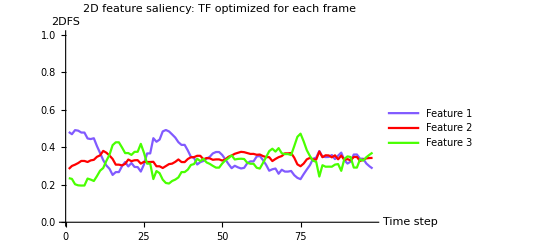

```mathematica
plots3[[4]]
```